## Math 578 Homework 2 Due: Sept 13 in class Prof. J. H. Chaudhry Student: Brad M. Philipbar

## Plots and code: https://github.com/bphilipbar/math578 are also attached.

## Problem 1)

Plot1, Below: Nx=10, Nt=51

Plot2, Below: Nx=20, Nt=51

-Graphics-

Plot3, Below: Nx=50, Nt=51

## Problem 3)

3 Plots, Below: 
Nx = 30  # NOT including the “fake” value on left
Ny = 30  # NOT including the “fake” value on bottom
Nt = 1000
tf = 1.01

figure 1: IC

figure 2: t = .01

figure 3: t = 1.01

Problem 4)

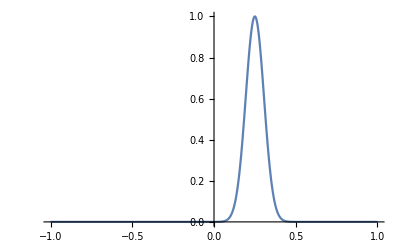

{{x→0.194098},{x→0.305902}}

{-(√(ⅇ/5))/8,(√(ⅇ/5))/8}

{-0.0921663,0.0921663}

```mathematica
f=Exp[-10 (4 x-1)^2];
Plot[f,{x,-1,1},PlotRange->All]
xSol=Solve[D[f,{x,2}]==0,x];(*optimize f'*)N[xSol] (*the second solution is clearly the one with the negative slope*)
t=Simplify[-1/D[f,x]/.xSol]
N[t]
```